# (Top Project - dim6 ( Ctw,Cbw,CHud ,C3phiq ) and dim 8 ( C1quWH3 , C1qdWH3 , C2q2H4D , C3 q2H4D ,CudH4D ) - Right Handed Decay width - SM , Dim 8 -- Dim 6^2 --lambda^-4 )

```mathematica
Quit[]
```

```mathematica
(* Activate FA/FC *)
$LoadFeynArts=True;
$FeynCalcStartupMessages=True;
<<FeynCalc`
$FAVerbose=0;
FAPatch[PatchModelsOnly->True];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll"];
```

Successfully patched FeynArts.

```mathematica
(* Load FR model *)
InitializeModel["/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"]
```

True

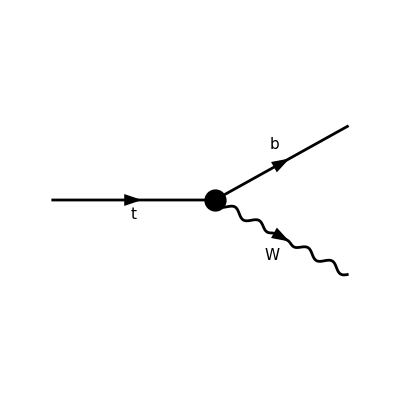

FeynArtsGraphics()(([] | Null | Null | Null | Null | Null))

```mathematica
(* Create diagrams *)
topo=CreateTopologies[0,1->2] (* # of loops = 0 *);

diag=InsertFields[topo,{F[9]}->{F[12], V[3]},InsertionLevel->{Particles},Model->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"];
Paint[diag,ColumnsXRows->{6,1},Numbering->None,SheetHeader->False,ImageSize->{800,200}]
```

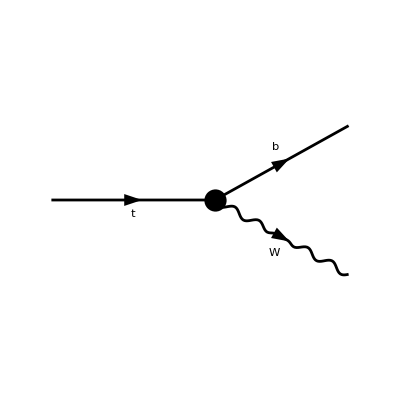

FeynArtsGraphics()(([]))

```mathematica
(* Diagram List *)
NofDiagrams=1;
lsD=Table[diag//DiagramDelete[#,Table[If[j≠i,j],{j,1,NofDiagrams}]/.Null->Sequence[]]&,{i,1,NofDiagrams}];
Paint[lsD[[1]],ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{200,100}]
```

```mathematica
(* Calculate amplitude *)
lsA0=Table[
FCFAConvert[CreateFeynAmp[lsD[[i]]],IncomingMomenta->{pt},OutgoingMomenta->{pb,pW},ChangeDimension->4,List->False,SMP->False,Contract->True,DropSumOver->True],
{i,1,NofDiagrams}];

lsA0=lsA0[[1]]//FeynAmpDenominatorExplicit//Simplify
(*%//TraditionalForm*)
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 gc145L Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^7+2 gc145R Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^6).(φ(OverBar[pt],FCGV(MT)))

```mathematica
gc145L = (FCGV["EL"]*(4*Lambda^4 + 2*C2q2H4D*vev^4 + C3q2H4D*vev^4 + 2*vev^4*Conjugate[C2q2H4D] + 4*Lambda^2*vev^2*Conjugate[C3phiq] - vev^4*Conjugate[C3q2H4D])*Conjugate[CKM3x3])/(4*Sqrt[2]*Lambda^4*sw);
gc145R = (FCGV["EL"]*(Lambda^4*vev^2*Conjugate[CHud] + vev^4*Conjugate[CudH4D]))/(2*Sqrt[2]*Lambda^4*sw);
sw=e/g;
```

```mathematica
lsA0//FullSimplify
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(8 e Lambda^4)ⅈ δ_Col1Col2 (-4 e vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW])-4 e vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 √2 g Conjugate[CKM3x3] FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^7 (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 Lambda^2 vev^2 Conjugate[C3phiq]+2 Lambda^4)+2 √2 g vev^2 FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^4 Conjugate[CHud]+vev^2 Conjugate[CudH4D])).(φ(OverBar[pt],FCGV(MT)))

```mathematica
(* Simplify *)
(* Setup the kinematics *)
SetMandelstam[s,t,u,pt,pb,pW,mpt,mpb,mpW];

rep0={EL->e,CW->cW,SW->sW,MW->mW,ME->0,MB->mb,MT->mt,
Pair[Momentum[pt],Momentum[pt]]->mt^2,
Pair[Momentum[pb],Momentum[pb]]->mb^2,
Pair[Momentum[pW],Momentum[pW]]->mW^2};
lsA=(lsA0//ReplaceAll@{FCGV[x_String]:>ToExpression[x]}(*//DiracSimplify*))/.rep0
```

-ⅈ (φ(OverBar[pb],mb)).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+(g Conjugate[CKM3x3] (γ̄·(ε̄)^*(pW)).(γ̄)^7 (2 vev^4 Conjugate[C2q2H4D]+2 C2q2H4D vev^4+4 Lambda^2 vev^2 Conjugate[C3phiq]-vev^4 Conjugate[C3q2H4D]+C3q2H4D vev^4+4 Lambda^4))/(2 √2)+(g (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^4 vev^2 Conjugate[CHud]+vev^4 Conjugate[CudH4D]))/(√2)).(φ(OverBar[pt],mt))

```mathematica
Fspin[x_]:=x//SUNFDeltaContract//FermionSpinSum[#,ExtraFactor->1/2]&//ReplaceAll[#,DiracTrace->TR]&
(lsAsq=(lsA*ComplexConjugate[lsA])//Simplify//Fspin//Contract)
```

```mathematica
lsAsqq=lsAsq/.{SUNN->Nc}//FullSimplify
```

1/(32 Lambda^8)Nc (4 g^2 vev^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) Lambda^8+8 g vev^2 Conjugate[CHud] (g Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+√2 mt (2 Conjugate[CbW] Lambda^4+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+mb Conjugate[CKM3x3] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))) Lambda^4+4 (g^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^8+2 √2 g mt (2 Conjugate[CbW] Lambda^4+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev^5+8 (2 vev Conjugate[CbW] Lambda^4+vev^3 Conjugate[C1qdWH3])^2 (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))-ⅈ ((OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)))+((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])) ((ε̄)^*(pW)·ε̄(pW))))+4 mb vev Conjugate[CKM3x3] (4 Conjugate[CbW] (-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-2 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) Lambda^4+2 g vev^3 Conjugate[CudH4D] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))+vev^2 Conjugate[C1qdWH3] (-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-4 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))+(Conjugate[CKM3x3])^2 (-16 g^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-64 √2 CtW g mt vev (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-16 ⅈ g^2 vev^4 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 √2 C1quWH3 g mt vev^3 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-64 √2 CtW g mt vev^3 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-256 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 g^2 vev^4 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C3q2H4D CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C1quWH3 g mt vev^5 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-256 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2+32 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+4 C2q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-3 C3q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-4 g^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-g^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-16 ⅈ √2 C1quWH3 g mt vev^7 Im(C3q2H4D) (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))-64 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW))-16 C2q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-16 ⅈ g^2 vev^8 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 g mt vev^7 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 ⅈ vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (4 vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW])+√2 g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+4 C3q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D)+(OverBar[pb]·ε̄(pW)) ((OverBar[pt]·(ε̄)^*(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·(ε̄)^*(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+(OverBar[pb]·(ε̄)^*(pW)) ((OverBar[pt]·ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·ε̄(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))

```mathematica
Quit[]
```

```mathematica
Pb={Eb,pb Sin[θ]Cos[ϕ],pb Sin[θ] Sin[ϕ],pb Cos[θ]};
pw={EW,-pb Sin[θ]Cos[ϕ],-pb Sin[θ] Sin[ϕ],-pb Cos[θ]};
pt={mt,0,0,0};
Eprh=1/(Sqrt[2]){0,-Cos[θ]Cos[ϕ]-I Sin[ϕ],-Cos[θ] Sin[ϕ]+I Cos[ϕ],Sin[θ]};
Epcrh=1/(Sqrt[2]){0,-Cos[θ]Cos[ϕ]+I Sin[ϕ],-Cos[θ] Sin[ϕ]-I Cos[ϕ],Sin[θ]};
```

```mathematica
MinkSP[vec1_,vec2_]:=Times[vec1[[1]],vec2[[1]]]-Times[vec1[[2]],vec2[[2]]]-Times[vec1[[3]],vec2[[3]]]-Times[vec1[[4]],vec2[[4]]]
```

```mathematica
(*Define Levi-Civita with provided function, (-1)for lower index of Levi-Civita *)
LeviCivita[indices__]:=-Module[{list={indices}},If[Length[list]≠4||DuplicateFreeQ[list]===False,0,Signature[list]]]
(*Contraction of Levi-Civita with 4 specific 4-vectors*)
LeviCivitaContraction[Pb_,pt_,Epclh_,Eplh_]:=Sum[LeviCivita[mu,nu,rho,sigma]*Pb[[mu+1]] pt[[nu+1]] Epclh[[rho+1]]*Eplh[[sigma+1]],{mu,0,3},{nu,0,3},{rho,0,3},{sigma,0,3}]//Simplify
```

```mathematica
Msqt=1/(32 Lambda^8)*Nc*(4*g^2*vev^4*Conjugate[CHud]^2*(I*LeviCivitaContraction[Pb,pt,Epcrh,Eprh]+MinkSP[Pb,Eprh]*MinkSP[pt,Epcrh]+MinkSP[Pb,Epcrh]*MinkSP[pt,Eprh]-MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh])*Lambda^8+8*g*vev^2*Conjugate[CHud]*(g*Conjugate[CudH4D]*(I*LeviCivitaContraction[Pb,pt,Epcrh,Eprh]+MinkSP[Pb,Eprh]*MinkSP[pt,Epcrh]+MinkSP[Pb,Epcrh]*MinkSP[pt,Eprh]-MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh])*vev^4+Sqrt[2]*mt*(2*Conjugate[CbW]*Lambda^4+vev^2*Conjugate[C1qdWH3])*(2*I*LeviCivitaContraction[Pb,pw,Epcrh,Eprh]+MinkSP[Pb,Eprh]*MinkSP[pw,Epcrh]+MinkSP[Pb,Epcrh]*MinkSP[pw,Eprh]-2*MinkSP[Pb,pw]*MinkSP[Epcrh,Eprh])*vev+mb*Conjugate[CKM3x3]*(I*Sqrt[2]*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*(2*LeviCivitaContraction[pt,pw,Epcrh,Eprh]+I*(MinkSP[pt,Eprh]*MinkSP[pw,Epcrh]+MinkSP[pt,Epcrh]*MinkSP[pw,Eprh]))+MinkSP[Epcrh,Eprh]*(2*g*Lambda^2*mt*Conjugate[C3phiq]*vev^2+2*Sqrt[2]*(2*CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[pt,pw]*vev+g*mt*(2*Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))*Lambda^4+4*(g^2*Conjugate[CudH4D]^2*(I*LeviCivitaContraction[Pb,pt,Epcrh,Eprh]+MinkSP[Pb,Eprh]*MinkSP[pt,Epcrh]+MinkSP[Pb,Epcrh]*MinkSP[pt,Eprh]-MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh])*vev^8+2*Sqrt[2]*g*mt*(2*Conjugate[CbW]*Lambda^4+vev^2*Conjugate[C1qdWH3])*Conjugate[CudH4D]*(2*I*LeviCivitaContraction[Pb,pw,Epcrh,Eprh]+MinkSP[Pb,Eprh]*MinkSP[pw,Epcrh]+MinkSP[Pb,Epcrh]*MinkSP[pw,Eprh]-2*MinkSP[Pb,pw]*MinkSP[Epcrh,Eprh])*vev^5+8*(2*vev*Conjugate[CbW]*Lambda^4+vev^3*Conjugate[C1qdWH3])^2*(2*I*LeviCivitaContraction[Pb,pw,Epcrh,Eprh]*MinkSP[pt,pw]+MinkSP[Pb,Eprh]*MinkSP[pw,Epcrh]*MinkSP[pt,pw]+MinkSP[Pb,Epcrh]*MinkSP[pw,Eprh]*MinkSP[pt,pw]+MinkSP[Pb,pw]*MinkSP[pt,Eprh]*MinkSP[pw,Epcrh]+MinkSP[Pb,pw]*MinkSP[pt,Epcrh]*MinkSP[pw,Eprh]-MinkSP[Pb,pt]*MinkSP[pw,Epcrh]*MinkSP[pw,Eprh]
-I*((LeviCivitaContraction[Pb,pt,Epcrh,Eprh]-I*(MinkSP[Pb,Eprh]*MinkSP[pt,Epcrh]+MinkSP[Pb,Epcrh]*MinkSP[pt,Eprh]))*MinkSP[pw,pw]
-LeviCivitaContraction[Pb,pt,pw,Eprh]*MinkSP[pw,Epcrh]+LeviCivitaContraction[Pb,pt,pw,Epcrh]*MinkSP[pw,Eprh])
+(MinkSP[Pb,pt]*MinkSP[pw,pw]-2*MinkSP[Pb,pw]*MinkSP[pt,pw])*MinkSP[Epcrh,Eprh]))+4*mb*vev*Conjugate[CKM3x3]*(4*Conjugate[CbW]*(-8*mt*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*(MinkSP[pw,Epcrh]*MinkSP[pw,Eprh]-MinkSP[pw,pw]*MinkSP[Epcrh,Eprh])-2*I*Sqrt[2]*g*LeviCivitaContraction[pt,pw,Epcrh,Eprh]*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2]*g*MinkSP[pt,Eprh]*MinkSP[pw,Epcrh]*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2]*g*(MinkSP[pt,Epcrh]*MinkSP[pw,Eprh]-2*MinkSP[pt,pw]*MinkSP[Epcrh,Eprh])*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))*Lambda^4+2*g*vev^3*Conjugate[CudH4D]*(I*Sqrt[2]*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*(2*LeviCivitaContraction[pt,pw,Epcrh,Eprh]+I*(MinkSP[pt,Eprh]*MinkSP[pw,Epcrh]+MinkSP[pt,Epcrh]*MinkSP[pw,Eprh]))+MinkSP[Epcrh,Eprh]*(2*g*Lambda^2*mt*Conjugate[C3phiq]*vev^2+2*Sqrt[2]*(2*CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[pt,pw]*vev+g*mt*(2*Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+vev^2*Conjugate[C1qdWH3]*(-16*mt*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*(MinkSP[pw,Epcrh]*MinkSP[pw,Eprh]-MinkSP[pw,pw]*MinkSP[Epcrh,Eprh])-4*I*Sqrt[2]*g*LeviCivitaContraction[pt,pw,Epcrh,Eprh]*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2*Sqrt[2]*g*(MinkSP[pt,Epcrh]*MinkSP[pw,Eprh]-2*MinkSP[pt,pw]*MinkSP[Epcrh,Eprh])*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2*Sqrt[2]*g*MinkSP[pt,Eprh]*MinkSP[pw,Epcrh]*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+vev^4*(C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+(Conjugate[CKM3x3])^2*(-16*g^2*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]*Lambda^8-32*g^2*vev^2*Conjugate[C3phiq]*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]*Lambda^6-64*Sqrt[2]*CtW*g*mt*vev*MinkSP[Pb,pw]*MinkSP[Epcrh,Eprh]*Lambda^6-128*I*CtW^2*vev^2*LeviCivitaContraction[Pb,pt,pw,Eprh]*MinkSP[pw,Epcrh]*Lambda^4+128*CtW^2*vev^2*MinkSP[Pb,pw]*MinkSP[pt,Eprh]*MinkSP[pw,Epcrh]*Lambda^4+128*I*CtW^2*vev^2*LeviCivitaContraction[Pb,pt,pw,Epcrh]*MinkSP[pw,Eprh]*Lambda^4+128*CtW^2*vev^2*MinkSP[Pb,pw]*MinkSP[pt,Epcrh]*MinkSP[pw,Eprh]*Lambda^4-128*CtW^2*vev^2*MinkSP[Pb,pt]*MinkSP[pw,Epcrh]*MinkSP[pw,Eprh]*Lambda^4-16*g^2*vev^4*Conjugate[C3phiq]^2*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]*Lambda^4-16*I*g^2*vev^4*Im[C3q2H4D]*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]*Lambda^4-32*Sqrt[2]*C1quWH3*g*mt*vev^3*MinkSP[Pb,pw]*MinkSP[Epcrh,Eprh]*Lambda^4-64*Sqrt[2]*CtW*g*mt*vev^3*Conjugate[C3phiq]*MinkSP[Pb,pw]*MinkSP[Epcrh,Eprh]*Lambda^4-256*CtW^2*vev^2*MinkSP[Pb,pw]*MinkSP[pt,pw]*MinkSP[Epcrh,Eprh]*Lambda^4+128*CtW^2*vev^2*MinkSP[Pb,pt]*MinkSP[pw,pw]*MinkSP[Epcrh,Eprh]*Lambda^4-32*g^2*vev^4*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]*Re[C2q2H4D]*Lambda^4-128*I*C1quWH3*CtW*vev^4*LeviCivitaContraction[Pb,pt,pw,Eprh]*MinkSP[pw,Epcrh]*Lambda^2+128*C1quWH3*CtW*vev^4*MinkSP[Pb,pw]*MinkSP[pt,Eprh]*MinkSP[pw,Epcrh]*Lambda^2+128*I*C1quWH3*CtW*vev^4*LeviCivitaContraction[Pb,pt,pw,Epcrh]*MinkSP[pw,Eprh]*Lambda^2+128*C1quWH3*CtW*vev^4*MinkSP[Pb,pw]*MinkSP[pt,Epcrh]*MinkSP[pw,Eprh]*Lambda^2-128*C1quWH3*CtW*vev^4*MinkSP[Pb,pt]*MinkSP[pw,Epcrh]*MinkSP[pw,Eprh]*Lambda^2-8*C3q2H4D*g^2*vev^6*Conjugate[C3phiq]*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]*Lambda^2+8*g^2*vev^6*Conjugate[C3phiq]*Conjugate[C3q2H4D]*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]*Lambda^2-32 Sqrt[2]*C3q2H4D*CtW*g*mt*vev^5*MinkSP[Pb,pw]*MinkSP[Epcrh,Eprh]*Lambda^2-32 Sqrt[2]*C1quWH3*g*mt*vev^5*Conjugate[C3phiq]*MinkSP[Pb,pw]*MinkSP[Epcrh,Eprh]*Lambda^2-256*C1quWH3*CtW*vev^4*MinkSP[Pb,pw]*MinkSP[pt,pw]*MinkSP[Epcrh,Eprh]*Lambda^2+128*C1quWH3*CtW*vev^4*MinkSP[Pb,pt]*MinkSP[pw,pw]*MinkSP[Epcrh,Eprh]*Lambda^2-32*g^2*vev^6*Conjugate[C3phiq]*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]*Re[C2q2H4D]*Lambda^2-64 Sqrt[2]*CtW*g*mt*vev^5*MinkSP[Pb,pw]*MinkSP[Epcrh,Eprh]*Re[C2q2H4D]*Lambda^2+32 Sqrt[2]*CtW*g*mt*vev^5*MinkSP[Pb,pw]*MinkSP[Epcrh,Eprh]*Re[C3q2H4D]*Lambda^2-32 I*C1quWH3^2*vev^6*LeviCivitaContraction[Pb,pt,pw,Eprh]*MinkSP[pw,Epcrh]+32*C1quWH3^2*vev^6*MinkSP[Pb,pw]*MinkSP[pt,Eprh]*MinkSP[pw,Epcrh]+32 I*C1quWH3^2*vev^6*LeviCivitaContraction[Pb,pt,pw,Epcrh]*MinkSP[pw,Eprh]+32*C1quWH3^2*vev^6*MinkSP[Pb,pw]*MinkSP[pt,Epcrh]*MinkSP[pw,Eprh]-32*C1quWH3^2*vev^6*MinkSP[Pb,pt]*MinkSP[pw,Epcrh]*MinkSP[pw,Eprh]+4*C2q2H4D^2*g^2*vev^8*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]-3*C3q2H4D^2*g^2*vev^8*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]-4*g^2*vev^8*Conjugate[C2q2H4D]^2*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]-g^2*vev^8*Conjugate[C3q2H4D]^2*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]-16 I Sqrt[2]*C1quWH3*g*mt*vev^7*Im[C3q2H4D]*MinkSP[Pb,pw]*MinkSP[Epcrh,Eprh]-64*C1quWH3^2*vev^6*MinkSP[Pb,pw]*MinkSP[pt,pw]*MinkSP[Epcrh,Eprh]+32*C1quWH3^2*vev^6*MinkSP[Pb,pt]*MinkSP[pw,pw]*MinkSP[Epcrh,Eprh]-16*C2q2H4D*g^2*vev^8*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]*Re[C2q2H4D]-16 I*g^2*vev^8*Im[C3q2H4D]*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]*Re[C2q2H4D]-32 Sqrt[2]*C1quWH3*g*mt*vev^7*MinkSP[Pb,pw]*MinkSP[Epcrh,Eprh]*Re[C2q2H4D]-I*LeviCivitaContraction[Pb,pt,Epcrh,Eprh]*(4*g^2*(Conjugate[C2q2H4D])^2*vev^8+8*g^2*Conjugate[C2q2H4D] *(2*Conjugate[C3phiq] *Lambda^2+C2q2H4D*vev^2)*vev^6+(g^2*(Conjugate[C3q2H4D])^2*vev^6-2*C3q2H4D*g^2*Conjugate[C3q2H4D] *vev^6+16*g^2*Lambda^4*(Conjugate[C3phiq])^2*vev^2+32*g^2*Lambda^4*Re[C2q2H4D]*vev^2+16 I*g^2*Im[C3q2H4D]*(Lambda^4+vev^4*Re[C2q2H4D])*vev^2+16*g^2*Lambda^2*Conjugate[C3phiq] *(2*Lambda^4+C2q2H4D*vev^4+I*vev^4*Im[C3q2H4D])-32*(2*CtW*Lambda^2+C1quWH3*vev^2)^2*MinkSP[pw,pw])*vev^2+g^2*(16*Lambda^8+(4*C2q2H4D^2+C3q2H4D^2)*vev^8))-
16 I*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*LeviCivitaContraction[Pb,pw,Epcrh,Eprh]*(4*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[pt,pw]+Sqrt[2]*g*mt*(2*Lambda^4+2*vev^2*Conjugate[C3phiq] *Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))
+4*C3q2H4D*g^2*vev^8*MinkSP[Pb,pt]*MinkSP[Epcrh,Eprh]*Re[C3q2H4D]+MinkSP[Pb,Eprh]*(MinkSP[pt,Epcrh]*(4*g^2*Conjugate[C2q2H4D]^2*vev^8+8*g^2*Conjugate[C2q2H4D]*(2*Conjugate[C3phiq]*Lambda^2+C2q2H4D*vev^2)*vev^6+(g^2*Conjugate[C3q2H4D]^2*vev^6-2*C3q2H4D*g^2*Conjugate[C3q2H4D]*vev^6+16*g^2*Lambda^4*Conjugate[C3phiq]^2*vev^2+32*g^2*Lambda^4*Re[C2q2H4D]*vev^2+16 I*g^2*Im[C3q2H4D]*(Lambda^4+vev^4*Re[C2q2H4D])*vev^2+16*g^2*Lambda^2*Conjugate[C3phiq]*(2*Lambda^4+C2q2H4D*vev^4+I*vev^4*Im[C3q2H4D])-32*(2*CtW*Lambda^2+C1quWH3*vev^2)^2*MinkSP[pw,pw])*vev^2+g^2*(16*Lambda^8+(4*C2q2H4D^2+C3q2H4D^2)*vev^8))+8*vev*MinkSP[pw,Epcrh]*(4*vev*MinkSP[pt,pw]*(2*CtW*Lambda^2+C1quWH3*vev^2)^2+Sqrt[2]*g*mt*(4*CtW*Lambda^6+2*C1quWH3*vev^2*Lambda^4+2*vev^2*(2*CtW*Lambda^2+C1quWH3*vev^2)*Conjugate[C3phiq]*Lambda^2+C1quWH3*C3q2H4D*vev^6+vev^4*(2 I*CtW*Im[C3q2H4D]*Lambda^2+2*(2*CtW*Lambda^2+C1quWH3*vev^2)*Re[C2q2H4D]-C1quWH3*vev^2*Re[C3q2H4D]))))+MinkSP[Pb,Epcrh]*(MinkSP[pt,Eprh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2MinkSP[pw,pw])vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[pw,Eprh]*(4 vev MinkSP[pt,pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq]Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))))//FullSimplify
```

1/(32 Lambda^8)mt Nc (32 (Eb+pb) (EW+pb)^2 vev^6 Conjugate[C1qdWH3]^2+128 Lambda^8 (Eb+pb) (EW+pb)^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^8 (Eb+pb) vev^4 Conjugate[CHud]^2+4 g^2 (Eb+pb) vev^8 Conjugate[CudH4D]^2+32 Lambda^4 (EW+pb) vev Conjugate[CbW] (4 mb (-EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^4 (Eb+pb) vev^2 Conjugate[CHud]+(Eb+pb) vev^4 Conjugate[CudH4D]-mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+16 (EW+pb) vev^3 Conjugate[C1qdWH3] (8 Lambda^4 (Eb+pb) (EW+pb) vev Conjugate[CbW]+4 mb (-EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^4 (Eb+pb) vev^2 Conjugate[CHud]+(Eb+pb) vev^4 Conjugate[CudH4D]-mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-8 g Lambda^4 vev^2 Conjugate[CHud] (-g (Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 g Lambda^4+(C2q2H4D+C3q2H4D) g vev^4+2 √2 (EW-pb) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D])))-8 g mb vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 g Lambda^4+(C2q2H4D+C3q2H4D) g vev^4+2 √2 (EW-pb) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D]))+Conjugate[CKM3x3]^2 (16 g^2 Lambda^8 (Eb-pb)+64 √2 CtW g Lambda^6 (-Eb+pb) (-EW+pb) vev+128 CtW^2 Lambda^4 (Eb-pb) (EW-pb)^2 vev^2+32 √2 C1quWH3 g Lambda^4 (-Eb+pb) (-EW+pb) vev^3+128 C1quWH3 CtW Lambda^2 (Eb-pb) (EW-pb)^2 vev^4+32 √2 C3q2H4D CtW g Lambda^2 (-Eb+pb) (-EW+pb) vev^5+32 C1quWH3^2 (Eb-pb) (EW-pb)^2 vev^6+g^2 (C3q2H4D^2 (Eb-3 pb)+4 C2q2H4D^2 (Eb+pb)) vev^8+g vev^2 (8 C2q2H4D Eb g vev^6 Conjugate[C2q2H4D]+4 g (Eb-pb) vev^6 Conjugate[C2q2H4D]^2+16 g Lambda^4 (Eb-pb) vev^2 Conjugate[C3phiq]^2-2 C3q2H4D Eb g vev^6 Conjugate[C3q2H4D]+g (Eb-pb) vev^6 Conjugate[C3q2H4D]^2+8 Lambda^2 (Eb-pb) Conjugate[C3phiq] (4 g Lambda^4+4 √2 (EW-pb) vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+4 vev^2 (8 √2 CtW Lambda^2 (Eb-pb) (EW-pb) vev (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+4 g Lambda^4 (Eb-pb) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+4 √2 C1quWH3 (Eb-pb) (EW-pb) vev^3 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+g vev^4 (-4 (C2q2H4D pb+ⅈ (-Eb+pb) Im[C3q2H4D]) Re[C2q2H4D]+C3q2H4D pb Re[C3q2H4D])))))

```mathematica
MsqtSM=Msqt/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

1/2 g^2 mt Nc (Eb-pb) Conjugate[CKM3x3]^2

```mathematica
EW=(mt^2+mw^2-mb^2)/(2 mt);
Eb=mt-EW;
(*pb=-pw;
pw=-(1/(2 mt)) Sqrt[(mt^2-(mw+mb)^2) (mt^2-(mw-mb)^2)];*)
```

```mathematica
Msqtotal=1/(32 Lambda^8)mt Nc (32 (Eb+pb) (EW+pb)^2 vev^6 Conjugate[C1qdWH3]^2+128 Lambda^8 (Eb+pb) (EW+pb)^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^8 (Eb+pb) vev^4 Conjugate[CHud]^2+4 g^2 (Eb+pb) vev^8 Conjugate[CudH4D]^2+32 Lambda^4 (EW+pb) vev Conjugate[CbW] (4 mb (-EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^4 (Eb+pb) vev^2 Conjugate[CHud]+(Eb+pb) vev^4 Conjugate[CudH4D]-mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+16 (EW+pb) vev^3 Conjugate[C1qdWH3] (8 Lambda^4 (Eb+pb) (EW+pb) vev Conjugate[CbW]+4 mb (-EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^4 (Eb+pb) vev^2 Conjugate[CHud]+(Eb+pb) vev^4 Conjugate[CudH4D]-mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-8 g Lambda^4 vev^2 Conjugate[CHud] (-g (Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 g Lambda^4+(C2q2H4D+C3q2H4D) g vev^4+2 √2 (EW-pb) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D])))-8 g mb vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 g Lambda^4+(C2q2H4D+C3q2H4D) g vev^4+2 √2 (EW-pb) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D]))+Conjugate[CKM3x3]^2 (16 g^2 Lambda^8 (Eb-pb)+64 √2 CtW g Lambda^6 (-Eb+pb) (-EW+pb) vev+128 CtW^2 Lambda^4 (Eb-pb) (EW-pb)^2 vev^2+32 √2 C1quWH3 g Lambda^4 (-Eb+pb) (-EW+pb) vev^3+128 C1quWH3 CtW Lambda^2 (Eb-pb) (EW-pb)^2 vev^4+32 √2 C3q2H4D CtW g Lambda^2 (-Eb+pb) (-EW+pb) vev^5+32 C1quWH3^2 (Eb-pb) (EW-pb)^2 vev^6+g^2 (C3q2H4D^2 (Eb-3 pb)+4 C2q2H4D^2 (Eb+pb)) vev^8+g vev^2 (8 C2q2H4D Eb g vev^6 Conjugate[C2q2H4D]+4 g (Eb-pb) vev^6 Conjugate[C2q2H4D]^2+16 g Lambda^4 (Eb-pb) vev^2 Conjugate[C3phiq]^2-2 C3q2H4D Eb g vev^6 Conjugate[C3q2H4D]+g (Eb-pb) vev^6 Conjugate[C3q2H4D]^2+8 Lambda^2 (Eb-pb) Conjugate[C3phiq] (4 g Lambda^4+4 √2 (EW-pb) vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+4 vev^2 (8 √2 CtW Lambda^2 (Eb-pb) (EW-pb) vev (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+4 g Lambda^4 (Eb-pb) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+4 √2 C1quWH3 (Eb-pb) (EW-pb) vev^3 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+g vev^4 (-4 (C2q2H4D pb+ⅈ (-Eb+pb) Im[C3q2H4D]) Re[C2q2H4D]+C3q2H4D pb Re[C3q2H4D])))))//FullSimplify
```

1/(64 Lambda^8 mt^2)Nc (8 (mb^2+mt^2-mw^2+2 mt pb) (-mb^2+mt^2+mw^2+2 mt pb)^2 vev^6 Conjugate[C1qdWH3]^2+32 Lambda^8 (mb^2+mt^2-mw^2+2 mt pb) (-mb^2+mt^2+mw^2+2 mt pb)^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^8 mt^2 (mb^2+mt^2-mw^2+2 mt pb) vev^4 Conjugate[CHud]^2+4 g^2 mt^2 (mb^2+mt^2-mw^2+2 mt pb) vev^8 Conjugate[CudH4D]^2+8 g Lambda^4 mt^2 vev^2 Conjugate[CHud] (g (mb^2+mt^2-mw^2+2 mt pb) vev^4 Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2+2 mt pb) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 Lambda^4 mt (mb^2-mw^2-mt (mt+2 pb)) vev Conjugate[CbW] (4 mb (mb^2-mt^2-mw^2+2 mt pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^4 (mb^2+mt^2-mw^2+2 mt pb) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2+2 mt pb) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+8 (mb^2-mw^2-mt (mt+2 pb)) vev^3 Conjugate[C1qdWH3] (4 Lambda^4 ((mb^2-mw^2)^2-mt^2 (mt+2 pb)^2) vev Conjugate[CbW]-4 mb mt (mb^2-mt^2-mw^2+2 mt pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g mt (Lambda^4 (mb^2+mt^2-mw^2+2 mt pb) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2+2 mt pb) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mt^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 g Lambda^4 mt+(C2q2H4D+C3q2H4D) g mt vev^4-√2 (mb^2-mt^2-mw^2+2 mt pb) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+2 g Lambda^2 mt vev^2 Conjugate[C3phiq]+g mt vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D]))+Conjugate[CKM3x3]^2 (8 (mb^2+mt^2-mw^2-2 mt pb) (-mb^2+mt^2+mw^2-2 mt pb)^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2+8 √2 g mt (mb^2+mt^2-mw^2-2 mt pb) (-mb^2+mt^2+mw^2-2 mt pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g^2 mt^2 (16 Lambda^8 (mb^2+mt^2-mw^2-2 mt pb)+16 (C2q2H4D+C3q2H4D) Lambda^4 (mb^2+mt^2-mw^2-2 mt pb) vev^4+((4 C2q2H4D^2+C3q2H4D^2) (mb^2+mt^2-mw^2)+2 (4 C2q2H4D^2-3 C3q2H4D^2) mt pb) vev^8)+g mt vev^2 (8 vev^2 (-√2 ((mb^2-mw^2)^2-mt^2 (mt-2 pb)^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4 (mb^2+mt^2-mw^2-2 mt pb)+C2q2H4D (mb^2+mt^2-mw^2) vev^4)) Conjugate[C2q2H4D]+4 g mt (mb^2+mt^2-mw^2-2 mt pb) vev^6 Conjugate[C2q2H4D]^2+16 g Lambda^4 mt (mb^2+mt^2-mw^2-2 mt pb) vev^2 Conjugate[C3phiq]^2-2 C3q2H4D g mt (mb^2+mt^2-mw^2) vev^6 Conjugate[C3q2H4D]+g mt (mb^2+mt^2-mw^2-2 mt pb) vev^6 Conjugate[C3q2H4D]^2+8 Lambda^2 (mb^2+mt^2-mw^2-2 mt pb) Conjugate[C3phiq] (-2 √2 (mb^2-mt^2-mw^2+2 mt pb) vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g mt (2 Lambda^4+C2q2H4D vev^4)+2 g mt vev^4 (Conjugate[C2q2H4D]+ⅈ Im[C3q2H4D]))-16 g mt vev^6 (2 C2q2H4D mt pb-ⅈ (mb^2+mt^2-mw^2-2 mt pb) Im[C3q2H4D]) Re[C2q2H4D]+8 vev^2 (√2 ((mb^2-mw^2)^2-mt^2 (mt-2 pb)^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (-2 Lambda^4 (mb^2+mt^2-mw^2-2 mt pb)+C3q2H4D mt pb vev^4)) Re[C3q2H4D])))

```mathematica
MsqtotalSM=Msqtotal/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

1/4 g^2 Nc (mb^2+mt^2-mw^2-2 mt pb) Conjugate[CKM3x3]^2

```mathematica
(*Compute decay width systematically*)
```

```mathematica
(*Define p*for the decay t->W+b*)
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
(*Define two-body phase space integral with p*substitution*)
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidthRight=Integrate[Msqtotal *dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar,Eb->(mb^2-mw^2+mt^2)/(2mt)}//FullSimplify
```

1/(1024 Lambda^8 mt^5 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (8 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^6 Conjugate[C1qdWH3]^2+32 Lambda^8 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^8 mt^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CHud]^2+4 g^2 mt^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^8 Conjugate[CudH4D]^2+8 g Lambda^4 mt^2 vev^2 Conjugate[CHud] (g (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 Lambda^4 mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CbW] (4 mb (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^4 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+8 (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^3 Conjugate[C1qdWH3] (4 Lambda^4 ((mb^2-mw^2)^2-(mt^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2) vev Conjugate[CbW]-4 mb mt (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g mt (Lambda^4 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mt^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 g Lambda^4 mt+(C2q2H4D+C3q2H4D) g mt vev^4-√2 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+2 g Lambda^2 mt vev^2 Conjugate[C3phiq]+g mt vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D]))+Conjugate[CKM3x3]^2 (8 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-16 √2 g mt^3 (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g^2 mt^2 (16 Lambda^8 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))+16 (C2q2H4D+C3q2H4D) Lambda^4 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4+((4 C2q2H4D^2+C3q2H4D^2) (mb^2+mt^2-mw^2)+(4 C2q2H4D^2-3 C3q2H4D^2) √((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^8)+g mt vev^2 (8 vev^2 (-√2 ((mb^2-mw^2)^2-(mt^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (-2 Lambda^4 √(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)+(mb^2+mt^2-mw^2) (2 Lambda^4+C2q2H4D vev^4))) Conjugate[C2q2H4D]+4 g mt (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^6 Conjugate[C2q2H4D]^2+16 g Lambda^4 mt (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[C3phiq]^2-2 C3q2H4D g mt (mb^2+mt^2-mw^2) vev^6 Conjugate[C3q2H4D]+g mt (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^6 Conjugate[C3q2H4D]^2+8 Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[C3phiq] (-2 √2 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g mt (2 Lambda^4+C2q2H4D vev^4)+2 g mt vev^4 (Conjugate[C2q2H4D]+ⅈ Im[C3q2H4D]))-16 g mt vev^6 (C2q2H4D √((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)-ⅈ (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Im[C3q2H4D]) Re[C2q2H4D]+8 vev^2 (√2 ((mb^2-mw^2)^2-(mt^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (-2 Lambda^4 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))+1/2 C3q2H4D √((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) vev^4)) Re[C3q2H4D])))

```mathematica
DecayWidthRightSM=DecayWidthRight/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 √((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Nc Conjugate[CKM3x3]^2)/(64 mt^3 π)

```mathematica
DecayWidthRight6SM8=Coefficient[DecayWidthRight,Lambda^-4]//FullSimplify
```

-1/(128 mt^3 π)√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2) Nc vev^2 (2 vev Conjugate[C1qdWH3] (8 (-mb^4-mt^2 (mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+mb^2 (2 mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))) vev Conjugate[CbW]+√2 g (mt (mb^2-mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) Conjugate[CKM3x3]))+2 Conjugate[CKM3x3] (2 g^2 mb mt vev^2 Conjugate[CudH4D]+Conjugate[CKM3x3] (-8 CtW^2 (mb^4+mt^2 (mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+mb^2 (-2 mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))))+2 √2 C1quWH3 g mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev+g vev (4 √2 CtW mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) Conjugate[C3phiq]+g (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[C3phiq]^2+g (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+4 vev^2 Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 C1quWH3 mt mw^2+√2 (C2q2H4D+C3q2H4D) g (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev+√2 g (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (Conjugate[C2q2H4D]-Re[C3q2H4D])))-g vev^3 Conjugate[CHud] (g (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[CudH4D]+2 mb Conjugate[CKM3x3] (√2 C1quWH3 (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+g mt vev (-C3q2H4D-2 Re[C2q2H4D]+Re[C3q2H4D]))))

```mathematica
(*Total Decay Width *)
```

```mathematica
DecayWidthTotal=1/(4096 Lambda^8 mt^7 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (16 g^2 mt^4 (-2 mw^4+(mb^2+mt^2) mw^2+(mb^2-mt^2)^2) vev^4 (Conjugate[CHud])^2 Lambda^8-32 g mt^4 vev^2 Conjugate[CHud] (12 √2 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW] Lambda^4+6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]-g (-2 mw^4+(mb^2+mt^2) mw^2+(mb^2-mt^2)^2) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (g mt (2 Conjugate[C3phiq] Lambda^2+vev^2 (Conjugate[C2q2H4D]-Re(C3q2H4D))) vev^2-√2 (mb^2-mt^2-mw^2) (2 CtW Lambda^2+C1quWH3 vev^2) vev+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4))) Lambda^4+16 mt^4 vev^2 (-32 mw^2 (mw^4+(mb^2+mt^2) mw^2-2 (mb^2-mt^2)^2) (Conjugate[CbW])^2 Lambda^8-24 √2 g mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D] Lambda^4-8 mw^2 (mw^4+(mb^2+mt^2) mw^2-2 (mb^2-mt^2)^2) vev^4 (Conjugate[C1qdWH3])^2+g^2 (-2 mw^4+(mb^2+mt^2) mw^2+(mb^2-mt^2)^2) vev^6 (Conjugate[CudH4D])^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 (mw^4+(mb^2+mt^2) mw^2-2 (mb^2-mt^2)^2) Conjugate[CbW] Lambda^4+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (-2 g Lambda^2 mt Conjugate[C3phiq] vev^2+√2 (mb^2-mt^2-mw^2) (2 CtW Lambda^2+C1quWH3 vev^2) vev-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))-mt (2 Conjugate[CbW] Lambda^4+vev^2 Conjugate[C1qdWH3]) (8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) mw^2+√2 g (-mb^2+mt^2+mw^2) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))+(Conjugate[CKM3x3])^2 (4 mt^4 (mb^2-mt^2+mw^2) ((mb^2-mt^2-mw^2) (16 Lambda^8+16 vev^4 (Conjugate[C3phiq])^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 (Conjugate[C2q2H4D])^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+16 ⅈ Im(C3q2H4D) Re(C2q2H4D))) g^2-48 √2 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) g-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2)-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-((16 Lambda^8+16 (C2q2H4D+C3q2H4D) vev^4 Lambda^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8) g^2)-vev^2 (4 (Conjugate[C2q2H4D])^2 vev^6+(Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 ⅈ Im(C3q2H4D) Re(C2q2H4D) vev^6+16 Lambda^4 (Conjugate[C3phiq])^2 vev^2+8 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D] vev^2-16 Lambda^4 Re(C3q2H4D) vev^2+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) g^2+32 mw^2 (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2)))
```

1/(4096 Lambda^8 mt^7 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (16 g^2 Lambda^8 mt^4 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+16 mt^4 vev^2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^4 Conjugate[C1qdWH3]^2-32 Lambda^8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]^2-24 √2 g Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^6 Conjugate[CudH4D]^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 Lambda^4 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-32 g Lambda^4 mt^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 g Lambda^2 mt vev^2 Conjugate[C3phiq]-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt (vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)+√2 g (-mb^2+mt^2+mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (4 mt^4 (mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (32 mw^2 (2 CtW Lambda^2 vev+C1quWH3 vev^3)^2-g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)-g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))

```mathematica
DecayWidthTotalSM=DecayWidthTotal/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 √(-((mb-mt-mw) (mb+mt-mw))) ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) √(mt^2-(mb+mw)^2) Nc Conjugate[CKM3x3]^2)/(64 mt^3 mw^2 π)

```mathematica
DecayWidthTotal6SM8=Coefficient[ DecayWidthTotal,Lambda^-4]//FullSimplify
```

1/(128 mt^3 mw^2 π)√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2) Nc vev^2 (-2 mw^2 vev Conjugate[C1qdWH3] (8 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev Conjugate[CbW]+3 √2 g (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))-12 mw^2 vev^2 Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 C1quWH3 mt mw^2-√2 g (mb^2-mt^2-mw^2) vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+2 Conjugate[CKM3x3] (-6 g^2 mb mt mw^2 vev^2 Conjugate[CudH4D]+Conjugate[CKM3x3] (-8 CtW^2 mw^6+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C2q2H4D]-2 mw^4 (4 CtW^2 (mb^2+mt^2)+3 √2 g mt vev (C1quWH3+2 CtW Conjugate[C3phiq])+g^2 vev^2 (C2q2H4D+C3q2H4D+Conjugate[C3phiq]^2-Re[C3q2H4D]))+mw^2 (16 CtW^2 (mb^2-mt^2)^2+6 √2 g mt (-mb+mt) (mb+mt) vev (C1quWH3+2 CtW Conjugate[C3phiq])+g^2 (mb^2+mt^2) vev^2 (C2q2H4D+C3q2H4D+Conjugate[C3phiq]^2-Re[C3q2H4D]))+g^2 (mb^2-mt^2)^2 vev^2 (C2q2H4D+C3q2H4D+Conjugate[C3phiq]^2-Re[C3q2H4D])))+g vev^3 Conjugate[CHud] (g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (√2 C1quWH3 (mb^2-mt^2-mw^2)+g mt vev (-C3q2H4D-2 Re[C2q2H4D]+Re[C3q2H4D]))))

```mathematica
FR=DecayWidthRight6SM8/DecayWidthTotal6SM8//FullSimplify
```

-((mw^2 (2 vev Conjugate[C1qdWH3] (8 (-mb^4-mt^2 (mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+mb^2 (2 mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))) vev Conjugate[CbW]+√2 g (mt (mb^2-mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) Conjugate[CKM3x3]))+2 Conjugate[CKM3x3] (2 g^2 mb mt vev^2 Conjugate[CudH4D]+Conjugate[CKM3x3] (-8 CtW^2 (mb^4+mt^2 (mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+mb^2 (-2 mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))))+2 √2 C1quWH3 g mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev+g vev (4 √2 CtW mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) Conjugate[C3phiq]+g (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[C3phiq]^2+g (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+4 vev^2 Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 C1quWH3 mt mw^2+√2 (C2q2H4D+C3q2H4D) g (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev+√2 g (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (Conjugate[C2q2H4D]-Re[C3q2H4D])))-g vev^3 Conjugate[CHud] (g (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[CudH4D]+2 mb Conjugate[CKM3x3] (√2 C1quWH3 (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+g mt vev (-C3q2H4D-2 Re[C2q2H4D]+Re[C3q2H4D])))))/(-2 mw^2 vev Conjugate[C1qdWH3] (8 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev Conjugate[CbW]+3 √2 g (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))-12 mw^2 vev^2 Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 C1quWH3 mt mw^2-√2 g (mb^2-mt^2-mw^2) vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+2 Conjugate[CKM3x3] (-6 g^2 mb mt mw^2 vev^2 Conjugate[CudH4D]+Conjugate[CKM3x3] (-8 CtW^2 mw^6+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C2q2H4D]-2 mw^4 (4 CtW^2 (mb^2+mt^2)+3 √2 g mt vev (C1quWH3+2 CtW Conjugate[C3phiq])+g^2 vev^2 (C2q2H4D+C3q2H4D+Conjugate[C3phiq]^2-Re[C3q2H4D]))+mw^2 (16 CtW^2 (mb^2-mt^2)^2+6 √2 g mt (-mb+mt) (mb+mt) vev (C1quWH3+2 CtW Conjugate[C3phiq])+g^2 (mb^2+mt^2) vev^2 (C2q2H4D+C3q2H4D+Conjugate[C3phiq]^2-Re[C3q2H4D]))+g^2 (mb^2-mt^2)^2 vev^2 (C2q2H4D+C3q2H4D+Conjugate[C3phiq]^2-Re[C3q2H4D])))+g vev^3 Conjugate[CHud] (g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (√2 C1quWH3 (mb^2-mt^2-mw^2)+g mt vev (-C3q2H4D-2 Re[C2q2H4D]+Re[C3q2H4D])))))

```mathematica
(* SM Limit*)
```

```mathematica
FRSM=DecayWidthRightSM/DecayWidthTotalSM//FullSimplify
```

-(mw^2 (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)))/((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4)

```mathematica
(*Define parameters and constants*)
sw=0.4834;e=0.31345;vev=246.2205;g=0.6483;mb=4.7;mt= 172; mw=79.8;CKM3x3=1;
FCGV["EL"]=e;
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
C1quWH3=1;
C1qdWH3=1;
C2q2H4D=1;
C3q2H4D=1;
CudH4D=1;
CHud=1;
C3phiq=1;
CtW=1;
CbW;
```

```mathematica
FR
```

-(6368.04 (-6.50704×10^13+492.441 (-4.4336×10^11-2.6999×10^12 Conjugate[CbW])-3.96254×10^14 Conjugate[CbW]))/(1.33267×10^18-3.13588×10^6 (-6.65215×10^11-2.99154×10^12 Conjugate[CbW])+3.62807×10^18 Conjugate[CbW])

```mathematica
FRSM
```

0.000365425

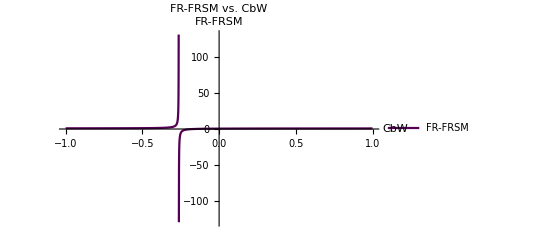

```mathematica
Plot[FR-FRSM,{CbW,-1,1},PlotStyle->{Darker[Purple]},AxesLabel->{"CbW","FR-FRSM"},PlotLabel->"FR-FRSM vs. CbW",PlotRange->All,PlotLegends->{"FR-FRSM"}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
C1quWH3=1;
C1qdWH3=1;
C2q2H4D=1;
C3q2H4D=1;
CudH4D=1;
CHud=1;
C3phiq=1;
CtW;
CbW=1;
```

```mathematica
FR
```

-((6368.04 (-2.00919×10^15+2 (4.0254×10^7+159.625 (-26966.9-11805.3 CtW)-618702. CtW^2)))/(1.64274×10^19+2 (6.87519×10^13-2.06589×10^12 CtW^2-8.11039×10^7 (50960.1+118424. CtW^2+116484. (1+2 CtW))+6368.04 (1.50873×10^9+1.39825×10^10 CtW^2+6.88696×10^9 (1+2 CtW)))))

```mathematica
FRSM
```

0.000365425

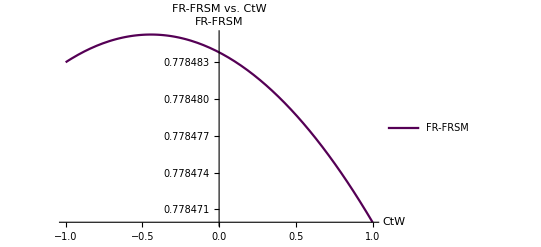

```mathematica
Plot[FR-FRSM,{CtW,-1,1},PlotStyle->{Darker[Purple]},AxesLabel->{"CtW","FR-FRSM"},PlotLabel->"FR-FRSM vs. CtW",PlotRange->All,PlotLegends->{"FR-FRSM"}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
C1quWH3=1;
C1qdWH3=1;
C2q2H4D=1;
C3q2H4D=1;
CudH4D=1;
CHud=1;
C3phiq;
CtW=1;
CbW=1;
```

```mathematica
FR
```

-((6368.04 (-2.00919×10^15+2 (3.96353×10^7+159.625 (-17977.9-11805.3 Conjugate[C3phiq]-8988.96 Conjugate[C3phiq]^2))))/(1.64274×10^19+2 (2.21516×10^13+2.22672×10^13 (1+Conjugate[C3phiq]^2)-8.11039×10^7 (118424.+116484. (1+2 Conjugate[C3phiq])+25480.1 (1+Conjugate[C3phiq]^2))+6368.04 (1.39825×10^10+6.88696×10^9 (1+2 Conjugate[C3phiq])+7.54365×10^8 (1+Conjugate[C3phiq]^2)))))

```mathematica
FRSM
```

0.000365425

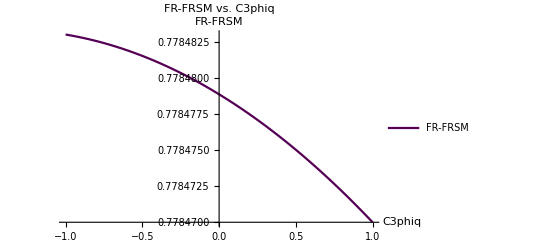

```mathematica
Plot[FR-FRSM,{C3phiq,-1,1},PlotStyle->{Darker[Purple]},AxesLabel->{"C3phiq","FR-FRSM"},PlotLabel->"FR-FRSM vs. C3phiq",PlotRange->All,PlotLegends->{"FR-FRSM"}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
C1quWH3=1;
C1qdWH3=1;
C2q2H4D=1;
C3q2H4D=1;
CudH4D=1;
CHud;
C3phiq=1;
CtW=1;
CbW=1;
```

```mathematica
FR
```

-(6368.04 (-3.96254×10^14+492.441 (-2.6999×10^12+0.916835 (555650.-4.83578×10^11 Conjugate[CHud]))-6.50704×10^13 Conjugate[CHud]))/(3.62858×10^18-3.13588×10^6 (-2.99154×10^12+2.7505 (337742.-2.41852×10^11 Conjugate[CHud]))+1.33216×10^18 Conjugate[CHud])

```mathematica
FRSM
```

0.000365425

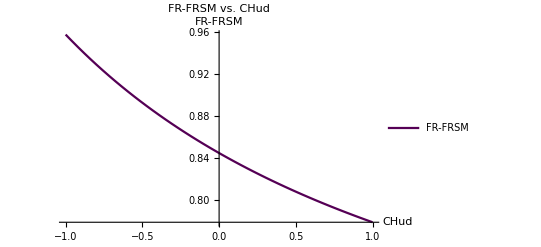

```mathematica
Plot[FR-FRSM,{CHud,-1,1},PlotStyle->{Darker[Purple]},AxesLabel->{"CHud","FR-FRSM"},PlotLabel->"FR-FRSM vs. CHud",PlotRange->All,PlotLegends->{"FR-FRSM"}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
C1quWH3=1;
C1qdWH3=1;
C2q2H4D=1;
C3q2H4D=1;
CudH4D=1;
CHud=1;
C3phiq=1;
CtW;
CbW;
```

```mathematica
FR
```

-((6368.04 (-6.50704×10^13+2 (4.0254×10^7+159.625 (-26966.9-11805.3 CtW)-618702. CtW^2)+492.441 (-4.4336×10^11-2.6999×10^12 Conjugate[CbW])-3.96254×10^14 Conjugate[CbW]))/(1.33216×10^18+2 (6.87519×10^13-2.06589×10^12 CtW^2-8.11039×10^7 (50960.1+118424. CtW^2+116484. (1+2 CtW))+6368.04 (1.50873×10^9+1.39825×10^10 CtW^2+6.88696×10^9 (1+2 CtW)))-3.13588×10^6 (-6.65215×10^11-2.99154×10^12 Conjugate[CbW])+3.62807×10^18 Conjugate[CbW]))

```mathematica
FRSM
```

0.000365425

```mathematica
Plot3D[Re[FR],{CtW,-1,1},{CbW,-1,1},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotPoints->100]
```

-Graphics3D-

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=1;
C3phiq=1;
CtW=1;
CbW=1;
C1quWH3;
C1qdWH3=1;
C2q2H4D=1;
C3q2H4D=1;
CudH4D=1;
```

```mathematica
FR
```

-((6368.04 (-1.54787×10^15-9.67718×10^6 (7.40975×10^6+9.4 (-54910.9-18028.7 C1quWH3))+2 (3.43885×10^7-942205. C1quWH3)+242498. (-1.80067×10^9+4.7 (2.66882×10^7+8.76242×10^6 C1quWH3))))/(1.14671×10^19+9.67718×10^6 (1.56645×10^11+179579. (-54910.9-50812.6 C1quWH3))-4.63271×10^9 (-9.00569×10^8+4.7 (1.62219×10^7+8.76242×10^6 C1quWH3))+2 (6.6686×10^13-8.11039×10^7 (169384.+116484. (2+C1quWH3))+6368.04 (1.54912×10^10+6.88696×10^9 (2+C1quWH3)))))

```mathematica
FRSM
```

0.000365425

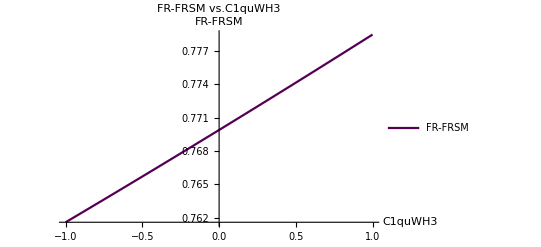

```mathematica
Plot[FR-FRSM,{C1quWH3,-1,1},PlotStyle->{Darker[Purple]},AxesLabel->{"C1quWH3","FR-FRSM"},PlotLabel->"FR-FRSM vs.C1quWH3",PlotRange->All,PlotLegends->{"FR-FRSM"}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=1;
C3phiq=1;
CtW=1;
CbW=1;
C1quWH3=1;
C1qdWH3;
C2q2H4D=1;
C3q2H4D=1;
CudH4D=1;
```

```mathematica
FR
```

-(6368.04 (-4.61324×10^14-1.54787×10^15 Conjugate[C1qdWH3]))/(4.96074×10^18+1.14671×10^19 Conjugate[C1qdWH3])

```mathematica
FRSM
```

0.000365425

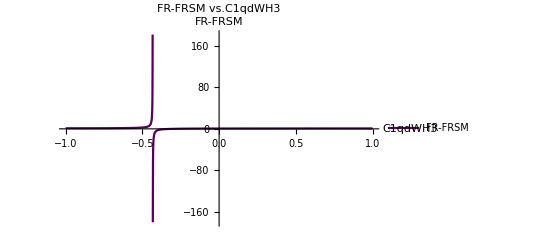

```mathematica
Plot[FR-FRSM,{C1qdWH3,-1,1},PlotStyle->{Darker[Purple]},AxesLabel->{"C1qdWH3","FR-FRSM"},PlotLabel->"FR-FRSM vs.C1qdWH3",PlotRange->All,PlotLegends->{"FR-FRSM"}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=1;
C3phiq=1;
CtW=1;
CbW=1;
C1quWH3=1;
C1qdWH3=1;
C2q2H4D;
C3q2H4D=1;
CudH4D=1;
```

```mathematica
FR
```

0.778835

```mathematica
FRSM
```

0.000365425

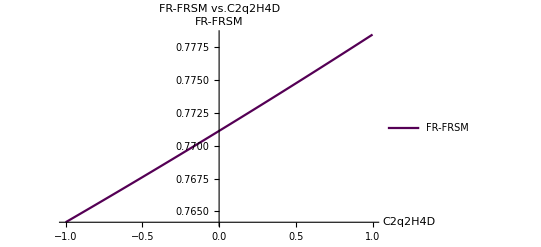

```mathematica
Plot[FR-FRSM,{C2q2H4D,-1,1},PlotStyle->{Darker[Purple]},AxesLabel->{"C2q2H4D","FR-FRSM"},PlotLabel->"FR-FRSM vs.C2q2H4D",PlotRange->All,PlotLegends->{"FR-FRSM"}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=1;
C3phiq=1;
CtW=1;
CbW=1;
C1quWH3=1;
C1qdWH3=1;
C2q2H4D=1;
C3q2H4D;
CudH4D=1;
```

```mathematica
FR
```

-((6368.04 (-1.54787×10^15+242498. (-1.80067×10^9+4.7 (8.76242×10^6+1.33441×10^7 (1+C3q2H4D)+1.33441×10^7 (1-Re[C3q2H4D])))+2 (3.96353×10^7+159.625 (-20794.2-8988.96 (2+C3q2H4D-Re[C3q2H4D])))-9.67718×10^6 (7.40975×10^6+9.4 (-18028.7+27455.5 (-2-C3q2H4D+Re[C3q2H4D])))))/(1.14671×10^19-4.63271×10^9 (-9.00569×10^8+4.7 (8.76242×10^6+8.11095×10^6 (2+C3q2H4D-Re[C3q2H4D])))+2 (2.21516×10^13-8.11039×10^7 (467875.+25480.1 (2+C3q2H4D-Re[C3q2H4D]))+6368.04 (3.46434×10^10+7.54365×10^8 (2+C3q2H4D-Re[C3q2H4D]))+2.22672×10^13 (2+C3q2H4D-Re[C3q2H4D]))+9.67718×10^6 (1.56645×10^11+179579. (-50812.6+27455.5 (-2-C3q2H4D+Re[C3q2H4D])))))

```mathematica
FRSM
```

0.000365425

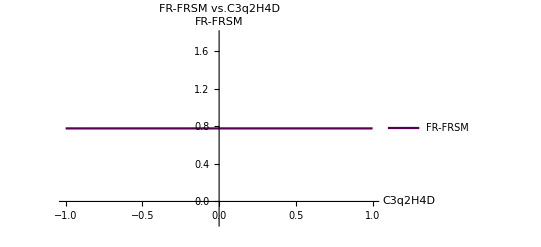

```mathematica
Plot[FR-FRSM,{C3q2H4D,-1,1},PlotStyle->{Darker[Purple]},AxesLabel->{"C3q2H4D","FR-FRSM"},PlotLabel->"FR-FRSM vs.C3q2H4D",PlotRange->All,PlotLegends->{"FR-FRSM"}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=1;
C3phiq=1;
CtW=1;
CbW=1;
C1quWH3=1;
C1qdWH3=1;
C2q2H4D=1;
C3q2H4D=1;
CudH4D;
```

```mathematica
FR
```

-((6368.04 (-1.54787×10^15+242498. (1.66618×10^8-1.80067×10^9 Conjugate[CudH4D])-9.67718×10^6 (-685632.+7.40975×10^6 Conjugate[CudH4D])+2 (-7.7499×10^6+4.11962×10^7 Conjugate[CudH4D])))/(1.14671×10^19+2 (2.55611×10^14-7.87016×10^11 Conjugate[CudH4D])-4.63271×10^9 (1.17426×10^8-9.00569×10^8 Conjugate[CudH4D])+9.67718×10^6 (-1.89857×10^10+1.56645×10^11 Conjugate[CudH4D])))

```mathematica
FRSM
```

0.000365425

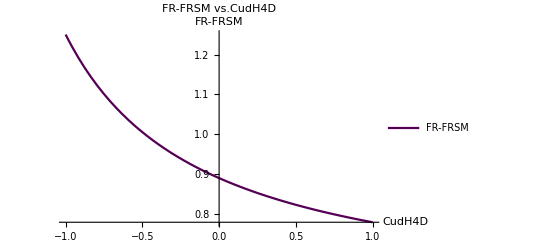

```mathematica
Plot[FR-FRSM,{CudH4D,-1,1},PlotStyle->{Darker[Purple]},AxesLabel->{"CudH4D","FR-FRSM"},PlotLabel->"FR-FRSM vs.CudH4D",PlotRange->All,PlotLegends->{"FR-FRSM"}]
```